{{-(-81 d^2 p-80 d^4 p)/(18 d^2),2 (-1+d) p},{2 (-1+d) p,2 p}}

{{1,-1/2},{-1/2,1/2}}

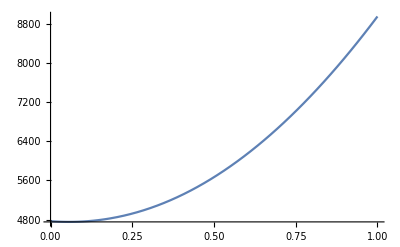

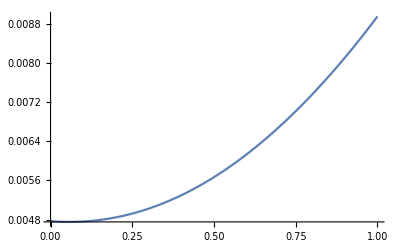

```mathematica
a1[d_,e_,phiAD_,phiAE_,p_]:=(e*phiAD+phiAE)/(1-d*e)
a2[d_,e_,phiAD_,phiAE_,p_]:=(d*phiAE+phiAD)/(1-d*e)
normAKmsq[d_,e_,phiAD_,phiAE_,p_]:=e*(1-phiAD)^2/(2*d)+d*(1-phiAE)^2/(2*e)
normAKpbsq[d_,e_,phiAD_,phiAE_,p_]:=(phiAD-d*a1[d,e,phiAD,phiAE,p]-phiAE+e*a2[d,e,phiAD,phiAE,p])^2+(phiAE-e*a2[d,e,phiAD,phiAE,p]+a2[d,e,phiAD,phiAE,p])^2+(a2[d,e,phiAD,phiAE,p]-a1[d,e,phiAD,phiAE,p])^2+(phiAD-d*a1[d,e,phiAD,phiAE,p]+a1[d,e,phiAD,phiAE,p])^2
normAKppsq[d_,e_,phiAD_,phiAE_,p_]:=(1-d*e)*(a1[d,e,phiAD,phiAE,p]^2+a2[d,e,phiAD,phiAE,p]^2)/2
tnormAKsq[d_,e_,phiAD_,phiAE_,p_]:=normAKmsq[d,e,phiAD,phiAE,p]+p*(normAKpbsq[d,e,phiAD,phiAE,p]+normAKppsq[d,e,phiAD,phiAE,p])
(*Solve[D[tnormAKsq[d,e,phiAD,phiAE,p],phiAD]==0 && D[tnormAKsq[d,e,phiAD,phiAE,p],phiAE]==0, {phiAD,phiAE}]*)
phiADstar[d_,e_,p_]:=(d^4 (7-8 e) e p-9 e^2 p+d^3 (e^3 (-1+p)+p-8 e p+7 e^2 p)+d e (-1+17 e^2 p)+d^2 e (e (2-9 p)+p+16 e^2 p-16 e^3 p))/(-9 e^2 p+16 d^4 e^2 (-1+p) p-d (e+81 e p^2+e^3 p (-17+80 p))+d^3 e ((17-80 p) p+16 e p (1+8 p)+e^2 (-1+2 p-193 p^2))+d^2 (-9 p+16 e^4 (-1+p) p+16 e^3 p (1+8 p)+2 e^2 (1-9 p+73 p^2)))
phiAEstar[d_,e_,p_]:=-((d e-2 d^2 e^2+d^3 e^3+9 d^2 p-17 d^3 e p-d e^2 p+9 d^2 e^2 p-16 d^3 e^2 p+16 d^4 e^2 p-e^3 p+8 d e^3 p-7 d^2 e^3 p-d^3 e^3 p-7 d e^4 p+8 d^2 e^4 p)/(-d e+2 d^2 e^2-d^3 e^3-9 d^2 p+17 d^3 e p-9 e^2 p-18 d^2 e^2 p+16 d^3 e^2 p-16 d^4 e^2 p+17 d e^3 p+16 d^2 e^3 p+2 d^3 e^3 p-16 d^2 e^4 p-81 d e p^2-80 d^3 e p^2+146 d^2 e^2 p^2+128 d^3 e^2 p^2+16 d^4 e^2 p^2-80 d e^3 p^2+128 d^2 e^3 p^2-193 d^3 e^3 p^2+16 d^2 e^4 p^2))
b1[d_,e_,phiBD_,phiBE_,p_]:=(e*phiBD+phiBE)/(1-d*e)
b2[d_,e_,phiBD_,phiBE_,p_]:= (d*phiBE+phiBD)/(1-d*e)
normBKmsq[d_,e_,phiBD_,phiBE_,p_]:=e*phiBD^2/(2*d)+d*phiBE^2/(2*e)
normBKpbsq[d_,e_,phiBD_,phiBE_,p_]:=(phiBD-d*b1[d,e,phiBD,phiBE,p]-phiBE+e*b2[d,e,phiBD,phiBE,p])^2+(phiBE-e*b2[d,e,phiBD,phiBE,p]+b2[d,e,phiBD,phiBE,p])^2+(1-b1[d,e,phiBD,phiBE,p]+b2[d,e,phiBD,phiBE,p])^2+(phiBD-d*b1[d,e,phiBD,phiBE,p]-1+b1[d,e,phiBD,phiBE,p])^2
normBKppsq[d_,e_,phiBD_,phiBE_,p_]:=(b1[d,e,phiBD,phiBE,p]^2+b2[d,e,phiBD,phiBE,p]^2)*(1-d*e)/2
tnormBKsq[d_,e_,phiBD_,phiBE_,p_]:=normBKmsq[d,e,phiBD,phiBE,p]+p*(normBKpbsq[d,e,phiBD,phiBE,p]+normBKppsq[d,e,phiBD,phiBE,p])
(*Solve[D[tnormBKsq[d,e,phiBD,phiBE,p],phiBD]==0 && D[tnormBKsq[d,e,phiBD,phiBE,p],phiBE]==0, {phiBD,phiBE}]*)
phiBDstar[d_,e_,p_]:=(4 (-1+d) d e p (d^2 e (-1+p)+8 e p-d (-1+(1-4 e)^2 p)))/(-9 e^2 p+16 d^4 e^2 (-1+p) p-d (e+81 e p^2+e^3 p (-17+80 p))+d^3 e ((17-80 p) p+16 e p (1+8 p)+e^2 (-1+2 p-193 p^2))+d^2 (-9 p+16 e^4 (-1+p) p+16 e^3 p (1+8 p)+2 e^2 (1-9 p+73 p^2)))
phiBEstar[d_,e_,p_]:=-((4 (e^2 p-d e^2 p-d e^3 p+d^2 e^3 p+9 d e p^2-9 d^2 e p^2-9 d^2 e^2 p^2+9 d^3 e^2 p^2+8 d e^3 p^2-16 d^2 e^3 p^2+8 d^3 e^3 p^2))/(-d e+2 d^2 e^2-d^3 e^3-9 d^2 p+17 d^3 e p-9 e^2 p-18 d^2 e^2 p+16 d^3 e^2 p-16 d^4 e^2 p+17 d e^3 p+16 d^2 e^3 p+2 d^3 e^3 p-16 d^2 e^4 p-81 d e p^2-80 d^3 e p^2+146 d^2 e^2 p^2+128 d^3 e^2 p^2+16 d^4 e^2 p^2-80 d e^3 p^2+128 d^2 e^3 p^2-193 d^3 e^3 p^2+16 d^2 e^4 p^2))

AdotAVEM[d_,e_,p_]:=tnormAKsq[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]
BdotBVEM[d_,e_,p_]:=tnormBKsq[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]
AdotBKm[d_,e_,p_]:=e*phiBDstar[d,e,p]*(-1+phiADstar[d,e,p])/(2*d)+d*phiBEstar[d,e,p]*(-1+phiAEstar[d,e,p])/(2*e)
AdotBKpb[d_,e_,p_]:=(phiADstar[d,e,p]-a1[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]*e-phiAEstar[d,e,p]+a2[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]*e)*(phiBDstar[d,e,p]-b1[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]*d-phiBEstar[d,e,p]+b2[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]*e)+(phiAEstar[d,e,p]-a2[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]*e-a2[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p])*(phiBEstar[d,e,p]-b2[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]*e+b2[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p])+(a1[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]-a2[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p])*(b1[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]-b2[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]-1)+(a1[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]*d-a1[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]-phiADstar[d,e,p])*(1-b1[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]-phiBDstar[d,e,p]+b1[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]*d)
AdotBKpp[d_,e_,p_]:=(a1[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]*b1[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p]+a2[d,e,phiADstar[d,e,p],phiAEstar[d,e,p],p]*b2[d,e,phiBDstar[d,e,p],phiBEstar[d,e,p],p])*(1-d*e)/2
AdotBVEM[d_,e_,p_]:= AdotBKm[d,e,p]+p*(AdotBKpb[d,e,p]+AdotBKpp[d,e,p])
AVEM[d_,e_,p_]:={{AdotAVEM[d,e,p],AdotBVEM[d,e,p]},{AdotBVEM[d,e,p],BdotBVEM[d,e,p]}} (*This is the VEM modified fine space matrix*)
(*Now IFEM*)
Den[d_,e_,p_]:=p*(d^2+e^2)+d*e*(d+e)*(1-p);
c1A[d_,e_,p_]:=(-p*(d^2+e^2)-e*(d+e)*(1-p))/Den[d,e,p];
c2A[d_,e_,p_]:=(-p*(d^2+e^2)-d*(d+e)*(1-p))/Den[d,e,p];
c3A[d_,e_,p_]:=p*(d^2+e^2)/Den[d,e,p];
c1B[d_,e_,p_]:=e^2*(1-d)*(1-p)/Den[d,e,p]-1;
c2B[d_,e_,p_]:=d*e*(1-e)*(1-p)/Den[d,e,p];
c3B[d_,e_,p_]:=d*e^2*(1-p)/Den[d,e,p];
c1C[d_,e_,p_]:=d*e*(1-d)*(1-p)/Den[d,e,p];
c2C[d_,e_,p_]:=d^2*(1-e)*(1-p)/Den[d,e,p]-1;
c3C[d_,e_,p_]:=d^2*e*(1-p)/Den[d,e,p];
Kp[d_,e_,p_]:=d*e/2;
Km[d_,e_,p_]:=1/2-d*e/2;
AdotAIF[d_,e_,p_]:= p*1*(c1A[d,e,p]^2+c2A[d,e,p]^2)*Kp[d,e,p]+1*((-c3A[d,e,p])^2+(-c3A[d,e,p])^2)*Km[d,e,p];
BdotBIF[d_,e_,p_]:= p*1*(c1B[d,e,p]^2+c2B[d,e,p]^2)*Kp[d,e,p]+1*((1-c3B[d,e,p])^2+(-c3B[d,e,p])^2)*Km[d,e,p];
AdotBIF[d_,e_,p_]:= p*1*(c1A[d,e,p]*c1B[d,e,p]+c2A[d,e,p]*c2B[d,e,p])*Kp[d,e,p]+1*((-c3A[d,e,p])*(1-c3B[d,e,p])+(-c3A[d,e,p])*(-c3B[d,e,p]))*Km[d,e,p];
AIFEM[d_,e_,p_]:={{AdotAIF[d,e,p],AdotBIF[d,e,p]},{AdotBIF[d,e,p],BdotBIF[d,e,p]}}; (*This is the IFE interpolation matrix*)
Arelative[d_,e_,p_]:=AIFEM[d,e,p].Inverse[AVEM[d,e,p]];
Releigen[d_,e_,p_]:=Max[Eigenvalues[Arelative[d,e,p]]];
(*Plot3D[Releigen[d,e,0.001],{d,0,1},{e,0,1}]*)
(*Relative EigenValue Plot for beta^{+}/beta^{-}=0.001*)
AVEMSimplify[d_,e_,p_]:={{(p (16 d^5 e p-e^2 (81+80 e^2) p+d^4 (e^2 (1-193 p)-80 p+128 e p)+d^3 e (-9+146 p+16 e^2 (-1+2 p)+2 e (1+64 p))+d^2 (-2 e+e^4 (1-193 p)+e^2 (50-160 p)-81 p+2 e^3 (1+64 p))+d e (-18-2 e+128 e^3 p+16 e^4 p+e^2 (-9+146 p))))/(2 (-9 e^2 p+16 d^4 e^2 (-1+p) p-d (e+81 e p^2+e^3 p (-17+80 p))+d^3 e ((17-80 p) p+16 e p (1+8 p)+e^2 (-1+2 p-193 p^2))+d^2 (-9 p+16 e^4 (-1+p) p+16 e^3 p (1+8 p)+2 e^2 (1-9 p+73 p^2)))),(2 (-1+d) p (4 e^4 (9+18 e-4 e^2) p^2+20 d^7 e^3 (9+8 e) (-1+p) p^2+d e^3 p (13+64 e^4 p+324 p^2+24 e^3 p (-13+32 p)-2 e^2 (1+9 p+72 p^2)+3 e (5+9 p+312 p^2))+d^6 e^2 p ((287-1592 p) p+2 e p (189+689 p)+e^2 (-29+378 p+227 p^2)-4 e^3 (7-22 p+463 p^2))+d^4 (81 p^2+450 e p^3+e^2 p (-51+430 p-1855 p^2)-32 e^7 p (1-5 p+116 p^2)-2 e^3 p (31+206 p+280 p^2)+2 e^6 p (5+222 p+2365 p^2)+e^5 (3-5 p+897 p^2-5211 p^3)+e^4 (3-62 p+372 p^2-2060 p^3))+d^2 e^2 (1+198 p^2-64 e^6 p^2+16 e^5 (29-120 p) p^2+6 e^2 p (-5+24 p+27 p^2)+2 e^4 p (3-131 p+216 p^2)-2 e^3 p (27-116 p+1928 p^2)+e (1+9 p+181 p^2+207 p^3))+d^3 e (256 e^7 p^2 (-1+3 p)+e^4 p (7-348 p-2272 p^2)+e p (13+127 p-198 p^2)+9 p (2+81 p^2)+4 e^6 p (-1+105 p+216 p^2)+e^5 p (71-627 p+4840 p^2)+e^3 (-3-11 p-731 p^2+743 p^3)+e^2 (-3+30 p-437 p^2+1750 p^3))+d^5 e (4 p^2 (-55+289 p)-2 e p^2 (117+1186 p)+e^3 p (77+21 p+306 p^2)+e^2 p (62-648 p+3075 p^2)+e^5 (-1+7 p-683 p^2+933 p^3)+e^4 (-1+32 p+107 p^2+2486 p^3))))/(-9 e^2 p+16 d^4 e^2 (-1+p) p-d (e+81 e p^2+e^3 p (-17+80 p))+d^3 e ((17-80 p) p+16 e p (1+8 p)+e^2 (-1+2 p-193 p^2))+d^2 (-9 p+16 e^4 (-1+p) p+16 e^3 p (1+8 p)+2 e^2 (1-9 p+73 p^2)))^2},{(2 (-1+d) p (4 e^4 (9+18 e-4 e^2) p^2+20 d^7 e^3 (9+8 e) (-1+p) p^2+d e^3 p (13+64 e^4 p+324 p^2+24 e^3 p (-13+32 p)-2 e^2 (1+9 p+72 p^2)+3 e (5+9 p+312 p^2))+d^6 e^2 p ((287-1592 p) p+2 e p (189+689 p)+e^2 (-29+378 p+227 p^2)-4 e^3 (7-22 p+463 p^2))+d^4 (81 p^2+450 e p^3+e^2 p (-51+430 p-1855 p^2)-32 e^7 p (1-5 p+116 p^2)-2 e^3 p (31+206 p+280 p^2)+2 e^6 p (5+222 p+2365 p^2)+e^5 (3-5 p+897 p^2-5211 p^3)+e^4 (3-62 p+372 p^2-2060 p^3))+d^2 e^2 (1+198 p^2-64 e^6 p^2+16 e^5 (29-120 p) p^2+6 e^2 p (-5+24 p+27 p^2)+2 e^4 p (3-131 p+216 p^2)-2 e^3 p (27-116 p+1928 p^2)+e (1+9 p+181 p^2+207 p^3))+d^3 e (256 e^7 p^2 (-1+3 p)+e^4 p (7-348 p-2272 p^2)+e p (13+127 p-198 p^2)+9 p (2+81 p^2)+4 e^6 p (-1+105 p+216 p^2)+e^5 p (71-627 p+4840 p^2)+e^3 (-3-11 p-731 p^2+743 p^3)+e^2 (-3+30 p-437 p^2+1750 p^3))+d^5 e (4 p^2 (-55+289 p)-2 e p^2 (117+1186 p)+e^3 p (77+21 p+306 p^2)+e^2 p (62-648 p+3075 p^2)+e^5 (-1+7 p-683 p^2+933 p^3)+e^4 (-1+32 p+107 p^2+2486 p^3))))/(-9 e^2 p+16 d^4 e^2 (-1+p) p-d (e+81 e p^2+e^3 p (-17+80 p))+d^3 e ((17-80 p) p+16 e p (1+8 p)+e^2 (-1+2 p-193 p^2))+d^2 (-9 p+16 e^4 (-1+p) p+16 e^3 p (1+8 p)+2 e^2 (1-9 p+73 p^2)))^2,(2 p (-5 e^2 p+12 d^4 e^2 (-1+p) p-d e (1+8 e p+45 p^2+e^2 p (-17+16 p))+d^3 e ((17-44 p) p+8 e p (1+17 p)+e^2 (-1+2 p-129 p^2))+d^2 (-9 p+16 e^3 p+16 e^4 (-1+p) p-72 e p^2+2 e^2 (1-5 p+71 p^2))))/(-9 e^2 p+16 d^4 e^2 (-1+p) p-d (e+81 e p^2+e^3 p (-17+80 p))+d^3 e ((17-80 p) p+16 e p (1+8 p)+e^2 (-1+2 p-193 p^2))+d^2 (-9 p+16 e^4 (-1+p) p+16 e^3 p (1+8 p)+2 e^2 (1-9 p+73 p^2)))}}
AVEMe0[d_,p_]:=AVEMSimplify[d,0,p]
AVEMe0[d,p]
AIFEM[d,0,p]
Releigene0[d_,p_]:=Max[Eigenvalues[AIFEM[d,0,p]*AVEMe0[d,p]]];
Plot[Releigene0[d,1000],{d,0,1}]
Plot[Releigene0[d,0.001],{d,0,1}]
```